# Coherent states

```mathematica
<<Wolfram`QuantumFramework`

creationAnnihilation[n_]:=Module[{ca,aa},
aa=QuantumOperator[SparseArray[Band[{1,2}]->√Range[n-1],{n,n}],n];
ca=aa["Dagger"];
{aa,ca}]

fockN[n_,d_]:= QuantumState[SparseArray[{n+1 -> 1}, d], d]
```

The number states |n⟩ have a uniform phase distribution from 0 to 2π, meaning there is not a defined phase. One may think that the classical limit is when the number of photons of a number state goes to ∞ , but that is not the case because ⟨n| E_x|n⟩  = 0 for any n. We seek states such the expectation of the field operator oscillates sinusoidally , we introduce the coherent states  that are the “most classical” states of the quantum harmonic oscillator.

## Eigenstates of the annihilation operator and minimum uncertainty

If we consider the superposition of number states that differ in ± 1, for example |ψ⟩ = c_n|n⟩ + c_(n+1)|n+1⟩ will have non zero expectation for the electric field operator. More generally, a superposition of all number states will also hold that property, the replacement of â and (â)^† by continuous variables  produces a classical field. A unique way to perform the replacement is to find eigenstates of annihilation operator , in other words solving the eigenvalue equation 
 where α can be in general complex because the operator is not Hermitian.

We can expand |α⟩ in the complete Fock basis 

And replacing in the eigenstate equation and comparing coefficients we can get a recurrence relation C_n √n = α C_(n-1) which is not difficult to solve and  a compact form can be expressed in function of C_0
      C_0 can be found from normalization yielding

Using this we can define a not normalized coherent state in a truncated Fock space, the normalization can be done when needed:
coherentTrunc[ d_]    :=      Not normalized coherent state with complex amplitude α (as QuantumState parameter)  in a Fock space of size d

```mathematica
coherentTrunc[d_]:= QuantumState[FoldList[Function[{prevCoeff,n},(α/Sqrt[n+1]) prevCoeff],1,Range[0,d-2]],d,"Parameters"->α]
```

Right annihilation operator eigenstate(we compare the amplitudes except the last one because we are using a finite basis):

```mathematica
αket =coherentTrunc[20]
```

QuantumState[…]

```mathematica
a = creationAnnihilation[20][[1]];
```

```mathematica
(a[αket]- α αket)["Amplitudes"]//Values //Most
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Analyzing the expected value of the electric field operator:

```mathematica
Ex = ⅈ √((h ω)/(2 Subscript[ϵ, 0] V))(a Exp[ⅈ(Dot[k,r]-ω t)]-a["Dagger"]Exp[-ⅈ(Dot[k,r]-ω t)]);
```

It is the same as  ⅈ √((ℏ ω)/(2 ϵ_0 V))(α ⅇ^(ⅈ (k.r - ω t))-α^*ⅇ^(-ⅈ (k.r - ω t))) resembling a classical field:

```mathematica
αrandom = 2 Exp[ⅈ Exp[RandomReal[{0,2π}]]];
```

```mathematica
With[{state=αket[αrandom]["Normalize"]},(state["Dagger"]@Ex@state)["Scalar"]]//FullSimplify//Chop
```

2.1839 (1. Cos[t ω-k.r]-0.823011 Sin[t ω-k.r]) √((h ω)/(V ϵ_0))

```mathematica
ⅈ √((h ω)/(2 Subscript[ϵ, 0] V)) (αrandom Exp[ⅈ (k.r-ω t)]-Conjugate[αrandom] Exp[-ⅈ (k.r-ω t)])//FullSimplify//Chop
```

2.1839 (1. Cos[t ω-k.r]-0.823011 Sin[t ω-k.r]) √((h ω)/(V ϵ_0))

Or in polar form α = |α| ⅇ^(ⅈ θ), ⟨ α | E_x(r, t) | α ⟩ = 2|α|√((h ω)/(2 ϵ_0 V)) sin(ω t - k. r-θ):

```mathematica
2 Abs[αrandom] √((h ω)/(2V Subscript[ϵ, 0])) Sin[ω t - Dot[k,r]-Arg[αrandom]]//TrigExpand//FullSimplify
```

2.1839 (1. Cos[t ω-k.r]-0.823011 Sin[t ω-k.r]) √((h ω)/(V ϵ_0))

It can be shown that ⟨ α | (E^2)_x(r, t) | α ⟩ =(h ω)/(2 ϵ_0 V) [1+4|α|^2 sin^2(ω t - k. r-θ)
so Δ E_x = √((h ω)/(2 ϵ_0 V))   is one of the expressions that corresponds to the vacuum fluctuations so the coherent state has field mean classical-like values and mean fluctuations of the vacuum

```mathematica
With[{state=αket[αrandom]["Normalize"]},(state["Dagger"]@Ex@Ex@state)["Scalar"]]//FullSimplify//Chop
```

(h ω (4.5+0.769435 Cos[2 t ω-2 k.r]-3.9253 Sin[2 t ω-2 k.r]))/(V ϵ_0)

```mathematica
√(%-(%%%)^2//FullSimplify //Chop[#,10^-6]&)
```

0.707107 √((h ω)/(V ϵ_0))

Another check is using the quadrature operators  X_i  from section 1.3 , the coherent states  minimize the uncertainty inequality with both quadrature uncertainties being the same. ⟨((ΔX_1))^2⟩_α= ⟨((ΔX_2))^2⟩_α=1/4

```mathematica
X1 := 1/2(a+a["Dagger"]);
X2 := ⅈ/2(a["Dagger"]-a);
```

```mathematica
quantumVariance[ψ_QuantumState,A_QuantumOperator]:= (ψ["Dagger"]@A@A@ψ)["Scalar"]-((ψ["Dagger"]@A@ψ)["Scalar"])^2
```

```mathematica
With[{s =coherentTrunc[20][αrandom]["Normalize"]},quantumVariance[s,#]&/@{X1,X2}]//Chop
```

{0.25,0.25}

The interpretation of α in a phase space context is α = ⟨ X_1⟩ + ⅈ ⟨ X_2⟩ obtained from seeking states that saturate the uncertainty inequality and solving certain eigenvalue equation given that [X_1,X_2] = ⅈ/2
Another physical interpretation of α is related to the photon number operator, it is easy to verify n^— = ⟨ α | n | α ⟩ = | α |^2

```mathematica
coh = coherentTrunc[20]["Normalize"];
```

The random α was chosen a complex number with norm 2, so the expectation returns 4

```mathematica
numberOp = a["Dagger"]@a;
(coh[αrandom]["Dagger"]@numberOp@coh[αrandom])["Scalar"]//Chop
```

4.

Δ n = √(|α|^4+|α|^2-(|α|^2)^2)  = √(n^—)

```mathematica
√quantumVariance[coh[αrandom],numberOp]//Chop
```

2.

This shows that the photon distribution follows a Poisson distribution, this is more clearly shown when calculating P_n the probability of measuring n photons. From the definition of coherent state in Fock basis it is not difficult to obtain P_n = e^(-|a|^2) (|a|^(2 n))/(√(n!)) = e^(- n^—) ((n^—)^n)/(√(n!)) 
The fractional uncertainty Δn/n^— =  1/√(n^—) decreases with increasing mean photon number. The phase distribution for a coherent state |α⟩ (α = |α| ⅇ^(ⅈ θ)) is 
  
For large |α| the Poisson distribution approximates to a Gaussian so a compact approximation can be derived
𝒫(ψ) ≈  √(2 |α|^2/π) exp(- 2 |α|^2(ψ - (θ))^2)

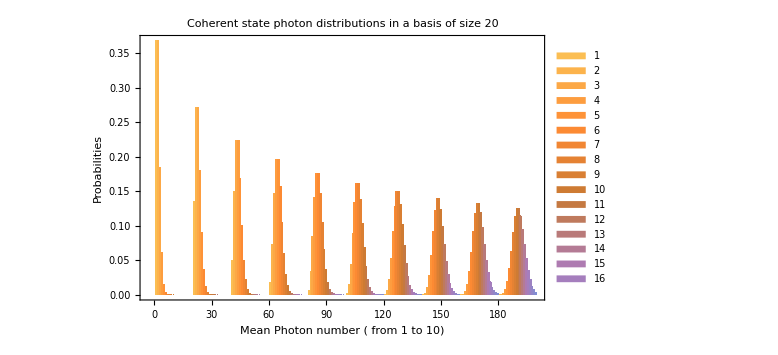

```mathematica
BarChart[Table[coh[√x]["Probabilities"]//Values,{x,1.,10}],]
```

NOTE: Since we are using a truncated basis it is worth noting that to appropriately describe a coherent state with amplitude α, the basis size should be around 
|α |^2+5 |α| (or higher) to include the tails of the  Poisson distribution

For this example |α| = √10the best size would be 10+5 √10 ≈ 25

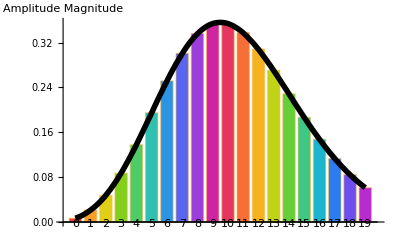

```mathematica
Show[coh[√10 Exp[ⅈ RandomReal[{0,2π}]]]["AmplitudePlot",ChartLegends->Automatic],Out[499],AxesLabel->{"","Amplitude Magnitude"}]
```

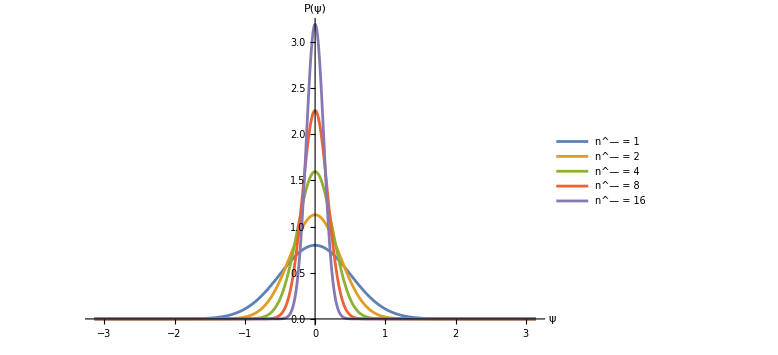

```mathematica
Plot[Evaluate[Table[√((2 Abs[x]^2)/π) Exp[-2 Abs[x]^2 (ψ-Arg[x])^2],{x,{√1,√2,√4,√8,√16}}]],{ψ,-π,π},]
```

So coherent states are quantum states with classical-like  features because:

Mean value of electric field has the form of a classical expression

Electric field fluctuations are those of the vacuum

Fluctuations in the photon number decrease when the mean photon number increases

Their phase becomes more localized when the mean photon number increases

## Displacement operator and displaced vacuum states

There exists an additional equivalent definition of a coherent state that is based on displacing the vacuum state , that can give more insight why coherent states have must have the uncertainty of the vacuum. The generator is the displacement operator that also has some nice algebraic properties, it is defined as:

and a coherent state can be build as

Using the disentangling theorem e^(Â + B̂) = e^(Â) e^(B̂) e^(-1/2 [A, B]) valid when [A, B] ≠ 0 but [A, [A, B]] = [B, [A, B] ] = 0 holds
⇒ D(α) = e^(-1/2 |α|^2)e^(α a^†)e^(- α^*a) so applying to vacuum
Expanding  e^(-α^*a) |0⟩ = ∑_k ((-α^*a)^k)/(k!) |0⟩ = |0⟩ because the annihilation operator and their powers kill the vacuum state except when k = 0
e^(α a^†) |0⟩ = ∑_(n=0)^∞ ((α a^†)^n)/(n!)|0⟩ = ∑_(n=0)^∞  α^n/(√(n!))|n⟩, because (a^†)^n |0⟩ = √(n!) |n⟩ so D(α) |0⟩ is exactly the same as the previous definition

Defining the displacement operator ( we will just work numerically because symbolically this definition can have really slow execution times):

```mathematica
Clear[disp]
disp[α_?NumberQ]:= Exp[α a["Dagger"]-α* a]
```

```mathematica
(disp[αrandom][]-coh[αrandom])["Amplitudes"]//Values
```

{-6.90244×10^-10,8.77259×10^-10+1.06591×10^-9 ⅈ,3.75542×10^-10-1.91585×10^-9 ⅈ,-1.98369×10^-9+1.07098×10^-9 ⅈ,2.08753×10^-9+8.51094×10^-10 ⅈ,-5.98666×10^-10-1.92519×10^-9 ⅈ,-9.03978×10^-10+1.37767×10^-9 ⅈ,1.22857×10^-9-1.33105×10^-10 ⅈ,-6.63582×10^-10-6.48964×10^-10 ⅈ,0.+3.4313×10^-10 ⅈ,1.2277×10^-9-8.45279×10^-10 ⅈ,4.37303×10^-9+1.25375×10^-9 ⅈ,7.55098×10^-9+1.74017×10^-8 ⅈ,-3.14091×10^-8+6.14101×10^-8 ⅈ,-2.30088×10^-7+5.04477×10^-8 ⅈ,-5.88887×10^-7-4.63052×10^-7 ⅈ,-4.95859×10^-8-2.22585×10^-6 ⅈ,4.69225×10^-6-4.04039×10^-6 ⅈ,0.0000159069+2.75169×10^-6 ⅈ,0.0000195429+0.0000343453 ⅈ}

Using a truncated basis has additional numeric error propagation because [a, a^†] is not exactly the identity. Using a bigger space size or reducing the magnitude of α can control the desired precision.

```mathematica
a = creationAnnihilation[35][[1]];
coh = coherentTrunc[35]["Normalize"];
```

```mathematica
(disp[αrandom][]-coh[αrandom])["Amplitudes"]//Values
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
αrandom = RandomComplex[{0,3+3I}];
```

D^†(α) = D (-α)

```mathematica
((disp[αrandom]["Dagger"]["Matrix"] - disp[-αrandom]["Matrix"])//Chop )["NonzeroPositions"]
```

{}

It is clear D^†(α) D(α) = D(α) D^†(α) = 1 , is a unitary operator

```mathematica
disp[αrandom]["UnitaryQ"]
```

True

Composing two displacement operators also has the form of a displacement operator times an overall phase factor 
 D(α) D(β) = e^(ⅈ Im( α β^*)) D(α + β) (can be proved with disentangling theorem)
 Intuitively if we do a displacement of α and then a displacement of β, the net displacement is α + β
  D(α) D(β) |0⟩ = D(α) |β⟩ = exp(ⅈ Im(α β*)) |α+β⟩

```mathematica
{αrandom,βrandom}= RandomComplex[{-2-2I,2+2I},2]
```

{-1.6409+1.57331 ⅈ,-0.533801+0.490973 ⅈ}

We consider a bigger size because are composing displacements:

```mathematica
a = creationAnnihilation[50][[1]];
coh = coherentTrunc[50]["Normalize"];
```

“AmplitudeList” returns non zero amplitudes, in this case all are zero so the states are the numerically the same

```mathematica
((disp[αrandom]@disp[βrandom][])-Exp[ⅈ Im[αrandom βrandom*]]coh[αrandom + βrandom]//Chop)["AmplitudeList"]
```

{}

## Wave packets and time evolution

```mathematica
{a,a†} = creationAnnihilation[20];
```

The position operator q̂ is defined, such that q̂ |q⟩ = q |q⟩ describes the position eigenstates:

```mathematica
q = √(h/(2m ω))X1;
```

The Fock states wave functions are :
  where ξ = q √(m ω/h)  and H_n are Hermite polynomials

The diagonal quantum harmonic oscillator Hamiltonian for a single mode field:

```mathematica
H = h ω (a†@a +1/2 QuantumOperator["I"[a["OutputDimension"]]]);
```

```mathematica
H["Formula"]
```

(h ω)/2 00+(3 h ω)/2 11+(5 h ω)/2 22+(7 h ω)/2 33+(9 h ω)/2 44+(11 h ω)/2 55+(13 h ω)/2 66+(15 h ω)/2 77+(17 h ω)/2 88+(19 h ω)/2 99+(21 h ω)/2 1010+(23 h ω)/2 1111+(25 h ω)/2 1212+(27 h ω)/2 1313+(29 h ω)/2 1414+(31 h ω)/2 1515+(33 h ω)/2 1616+(35 h ω)/2 1717+(37 h ω)/2 1818+(39 h ω)/2 1919

We create an evolution operator to evolve the states at any time:

```mathematica
QOE=QuantumOperator[QuantumEvolve[H/h,None,t],"Parameters"->t];
```

## Generation of coherent states

## More properties of coherent states

## Phase space picture of coherent states

## Phase space probability distributions for density operators

## Characteristic functions